```mathematica
CarlemanMatrix[f_,{x_,x0_,{m_Integer,n_Integer}}]:=
Prepend[Table[
If[k==0,
Function[x,f][x0]^j,
BellY[
Table[{FactorialPower[j,i] Which[#2==0,1,#1==0,0,True,#1^#2]&[Function[x,f][x0],j-i],Derivative[i][Function[x,f]][x0]},{i,k}]]/k!],
{j,m},
{k,0,n}],
UnitVector[n+1,1]]

CarlemanMatrix[f_,{x_,x0_,m_Integer}]:=CarlemanMatrix[f,{x,x0,{m,m}}]
```

```mathematica
(* produces a column matrix {1, f(x), ... f(x)^m} *)
EvaluateCarlemanPowers[mat_?MatrixQ,x_, m_Integer] := Dot[mat,Transpose[{x^#&/@Range[0,m]}]]
(* produces f(x) *)
EvaluateCarleman[mat_?MatrixQ,x_, m_Integer] := EvaluateCarlemanPowers[mat,x,m][[2,1]]
```

```mathematica
adda=CarlemanMatrix[a+x, {x, 0 , 2}]//Simplify;
adda//MatrixForm
```

(1 | 0 | 0
a | 1 | 0
a^2 | 2 a | 1)

```mathematica
sqrtAdda = MatrixPower[adda, 1/2];
sqrtAdda//MatrixForm
```

(1 | 0 | 0
a/2 | 1 | 0
a^2/4 | a | 1)

```mathematica
EvaluateCarleman[#,x,2]&/@{adda,sqrtAdda}
```

{a+x,a/2+x}

```mathematica
(* note: 1st-3rd order approximations are imperfect *)
EvaluateCarleman[CarlemanMatrix[x^4+2x^2, {x, 0 , #}],x,#]&/@Range[1,10]
```

{0,2 x^2,2 x^2,2 x^2+x^4,2 x^2+x^4,2 x^2+x^4,2 x^2+x^4,2 x^2+x^4,2 x^2+x^4,2 x^2+x^4}

```mathematica
EvaluateCarleman[CarlemanMatrix[Sin[x], {x, 0 , #}],x,#]&/@Range[1,10]
```

{x,x,x-x^3/6,x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}

```mathematica
sqrc = CarlemanMatrix[x^2, {x, 0, 2}];
sqrc//MatrixForm
```

(1 | 0 | 0
0 | 0 | 1
0 | 0 | 0)

```mathematica
MatrixPower[sqrc, 1/2]
```

MatrixPower[{{1,0,0},{0,0,1},{0,0,0}},1/2]

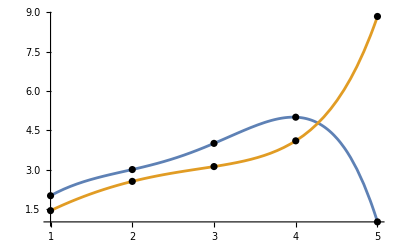

```mathematica
(* Can we find the square roots of permutations this way? *)
perm={2,3,4,5,1}; (* square root is {4,5,1,2,3} *)
fitRes=5;
poly = Fit[perm,x^#&/@Range[0,fitRes],x];
matRes=10;
polysqrt=EvaluateCarleman[MatrixPower[CarlemanMatrix[poly,{x,0,matRes}],1/2],x,matRes];
Show[Plot[{poly,polysqrt},{x,1,Length[perm]}],
ListPlot[{perm,Map[polysqrt/.x->#&,Range[5]]},PlotStyle->Black]]
```